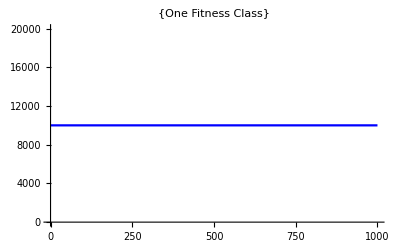

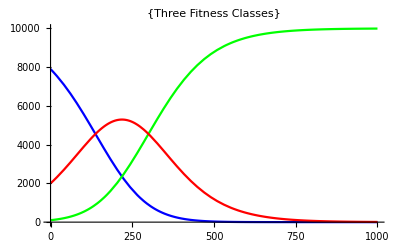

```mathematica
(* Testing SystemSolver, SolveDiffEqs *)
{Δc1,Δc2,popsize,timestep}={0.01,0.02,10^4,1000}; 
(* Testing system solver for one fitness class *)
genotypes={{1,1}};
genotypeabundances={10^4};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class"}]
(* Testing system solver for three fitness class *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4-100-2000,100,2000};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes"}]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Testing module that checks for new mutations, NextMutation *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep}={0,100}; 
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
```

```mathematica
getNextMutants[genotypes]
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,starttime,timestep]
```

{{{4,1},{{6,1}},0,0},{{3,2},{{5,1},{6,2}},0,0},{{2,3},{{3,1},{5,2}},0,0},{{1,4},{{3,2}},0,0}}

{30.9401,{{1,4}},True,0.0393006,{{3,2}}}

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension for first trait *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,0 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose}={0,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{2,1},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-0x10pn4_exp001.m",results];
```

mean substitutional load = 0.0351617

mean q = 3.51617

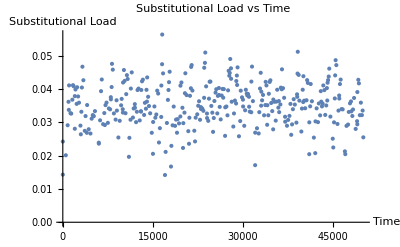

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-0x10pn4_exp001.m"];
meansubload1=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload1];
Print["mean q = ",meansubload1/Δc1];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check Evolution in 1 dimension for second trait *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,0 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,50000}; 
{fulldata,verbose,veryverbose}={0,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 0 in  No Evolution Regime  with expected time scale 0 and rate of adaptation 0

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-0x10pn4_U2-1x10pn4_exp002.m",results];
```

mean substitutional load = 0.0598228

mean q = 2.99114

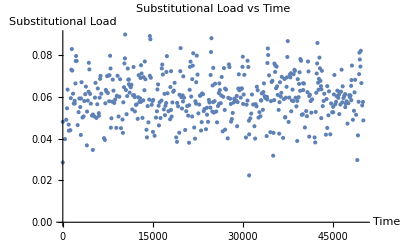

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-0x10pn4_U2-1x10pn4_exp002.m"];
meansubload2=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
Print["mean substitutional load = ",meansubload2];
Print["mean q = ",meansubload2/Δc2];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
```

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store only summary data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose}={0,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m",results];
```

mean substitution load = 0.0579544

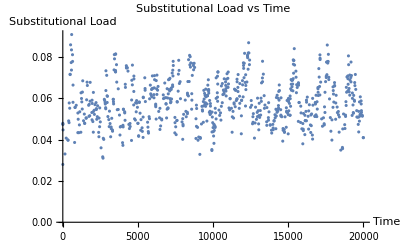

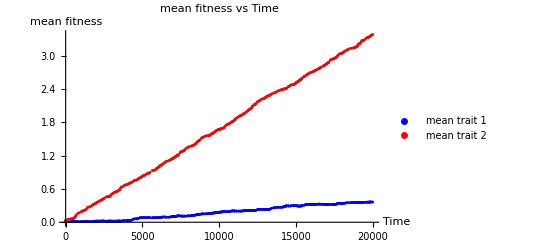

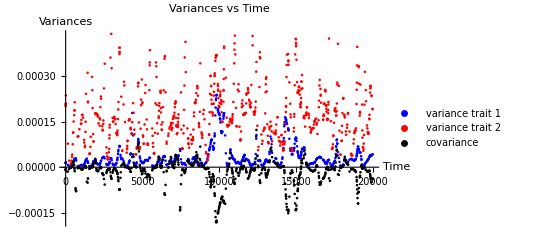

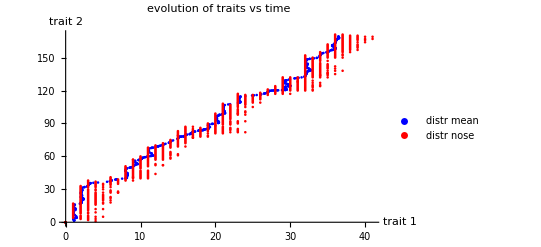

```mathematica
(* Plot Results of Simulation *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m"];
meansubload=Mean[Table[results[[i]][[9]],{i,1,Length[results]}]];
timesAndLoads=Table[{results[[i]][[1]],results[[i]][[9]]},{i,Length[results]}];
timesAndMean1=Table[{results[[i]][[1]],results[[i]][[2]]},{i,1,Length[results]}];
timesAndMean2=Table[{results[[i]][[1]],results[[i]][[3]]},{i,1,Length[results]}];
timesAndVar1=Table[{results[[i]][[1]],results[[i]][[6]]},{i,1,Length[results]}];
timesAndVar2=Table[{results[[i]][[1]],results[[i]][[7]]},{i,1,Length[results]}];
timesAndCov=Table[{results[[i]][[1]],results[[i]][[5]]},{i,1,Length[results]}];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
Print["mean substitution load = ",meansubload];
ListPlot[timesAndLoads,AxesLabel->{"Time","Substitutional Load"},PlotLabel->"Substitutional Load vs Time"]
ListPlot[{timesAndMean1,timesAndMean2},PlotStyle->{Blue,Red},PlotLegends->{"mean trait 1","mean trait 2"},AxesLabel->{"Time","mean fitness"},PlotLabel->"mean fitness vs Time"]
ListPlot[{timesAndVar1,timesAndVar2,timesAndCov},PlotStyle->{Blue,Red,Black},PlotLegends->{"variance trait 1","variance trait 2","covariance"},AxesLabel->{"Time","Variances"},PlotLabel->"Variances vs Time"]
ListPlot[{mean2mean,noseTravel},PlotStyle->{Blue,Red},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->"evolution of traits vs time"]
```

```mathematica
(* Generate animation of details evolution of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.m"];
mean2mean=Table[{results[[i]][[2]]/Δc1,results[[i]][[3]]/Δc2},{i,1,Length[results]}];
noseTravel=Table[results[[i]][[12]],{i,1,Length[results]}];
plots=Table[ListPlot[{mean2mean[[1;;i]],noseTravel[[1;;i]]},PlotStyle->{Black,Red},PlotRange->{{0,60},{0,150}},PlotLegends->{"distr mean","distr nose"},AxesLabel->{"trait 1","trait 2"},PlotLabel->{"evolution of traits vs time"}],{i,1,Length[mean2mean]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.avi",plots]
```

~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp003.avi

```mathematica
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* ---------------------------------------------------------------------------------------------------------------------- *)
(* Check evolution in 2 dimensions and store full data *)
(* simulation parameters *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
{starttime,timestep,maxtime}={0,1000,20000}; 
{fulldata,verbose,veryverbose}={1,False,False};
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Set initial genotypes and their abundances *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
(* Run simulation *)
SeedRandom[7];
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m",results];
```

```mathematica
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
results[[1]]
```

{0,{{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}},{507937.,253968.,126984.,63492.1,31746.,15873.},1.12698,1.53968,{0,0}}

```mathematica
(* Analyze Motion of blob *)
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.m"];
blob=results[[;;,{2,4,5}]];
Do[Do[
blob[[i]][[1]][[j]]=blob[[i]][[1]][[j]]-blob[[i]][[2]];
,{j,1,Length[blob[[i]][[1]]]}];
blob[[i]][[3]]=If[blob[[i]][[3]]=={0,0},{0,0},blob[[i]][[3]]-blob[[i]][[2]]];
,{i,1,Length[blob]}]
plots=Table[ListPlot[{blob[[i]][[1]],{blob[[i]][[3]]}},PlotStyle->{Black,Red},PlotRange->{{-5,7},{-5,7}},PlotMarkers->{Automatic,Large},PlotLegends->{"Fitness Classes","Mutant Fitness Class"},AxesLabel->{"trait 1","trait 2"},PlotLabel->{Evolution of blob}],{i,1,Length[blob]}];
Export["~/Documents/kgrel2d/plots/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.avi",plots];
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Export::errelem: The Export element GraphicsList contains a malformed data structure and could not be exported to AVI format.

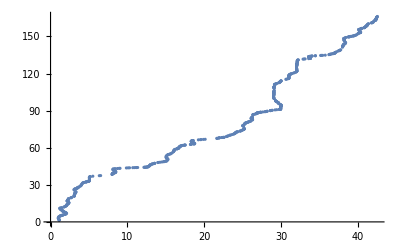

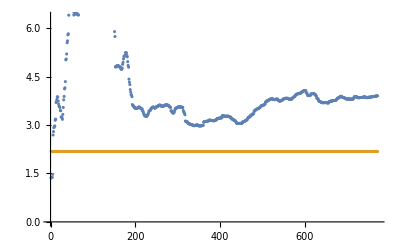

```mathematica
(* Examine Trajectories of Trait Mean Fitnesses *)
{Δc1,Δc2,U1,U2,popsize}={0.01,0.02,2 10^-4,1 10^-4,10^6};
results=Import["~/Documents/kgrel2d/data/simtest/simtest_N-10p6_c1-0d01_c2-0d02_U1-2x10pn4_U2-1x10pn4_exp004.dat"];
mean2mean=Table[({results[[i]][[3]]}.results[[i]][[2]])[[1]]/popsize,{i,1,Length[results]}];
meanratio=Table[mean2mean[[i]][[2]]/mean2mean[[i]][[1]],{i,1,Length[mean2mean]}];
velocityratio=Table[(Δc2^2(2 Log[popsize Δc2]-Log[Δc2/U2])/Log[Δc2/U2]^2)/(Δc1^2(2 Log[popsize Δc1]-Log[Δc1/U1])/Log[Δc1/U1]^2),{i,1,Length[mean2mean]}];
ListPlot[mean2mean,PlotLabel->{"mean fit trait 2 vs mean fit trait 1"},AxesLabel->{"trait 1 mean fit","trait 2 mean fit"}]
ListPlot[{meanratio,velocityratio},PlotLegends->{"ratio of mean fitnesses","ratio of theor-velocities"},PlotLabel->{"(mean-fit-2 / mean-fit-1) vs time"},AxesLabel->{"time","ratio"}]
```

```mathematica
(* simulation parameters *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=1000; 
maxtime=60000;
fulldata=0;
verbose=False;
veryverbose=False;
(* Check Regimes *)
printRegimeDetails[Δc1,Δc2,U1,U2,popsize];
(* Testing two trait evolution *)
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

Trait 1 q = 4.70874 in Concurrent Mutations Regime with expected time scale 105.481 and rate of adaptation 0.0000948035

Trait 2 q = 3.73835 in Concurrent Mutations Regime with expected time scale 96.7428 and rate of adaptation 0.000206734

```mathematica
ParallelDo[
results=RunSimulationCheckEachMutation2[popsize,Δc1,Δc2,U1,U2,maxtime,timestep,genotypes,genotypeabundances][[2]][[1]];
Export["~/Documents/kgrel2d/data/convtest/convtest_N-10p6_c1-0d01_c2-0d02_U1-1x10pn4_U2-2x10pn4_exp"<>ToString[i]<>".dat",results,"Data"];
Print["exp ",i];
,{i,2,35}];
```

0.647534

7.40436

0.087453

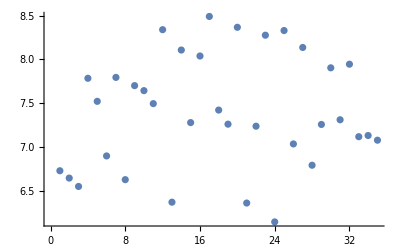

```mathematica
(* Analyzez convergence data *)
meanratios=Table[0,{i,1,35}];
Do[
results=Import["~/Documents/kgrel2d/data/convtest/convtest_N-10p6_c1-0d01_c2-0d02_U1-1x10pn4_U2-2x10pn4_exp"<>ToString[i]<>".dat"];
meanratios[[i]]=results[[-1]][[3]]/results[[-1]][[2]];
,{i,1,35}];
StandardDeviation[meanratios]
Mean[meanratios]
StandardDeviation[meanratios]/Mean[meanratios]
ListPlot[meanratios]
```